## Linear potential

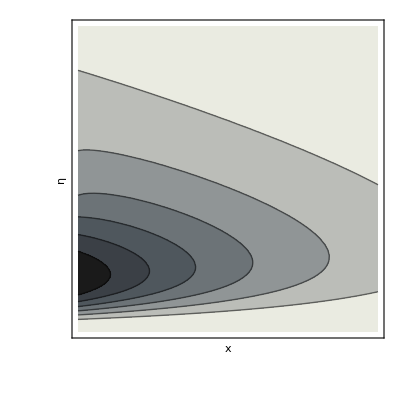

```mathematica
Δξ[θ_,θ0_]:=Log[θ/θ0]-θ+θ0
θ0[θ_,Δ_?NumericQ]:=θ0/.FindRoot[Δξ[θ,θ0]==Δ,{θ0,1+θ}]//Re//Quiet
p0[θ0_,β_]:=√(β/(2π))Exp[-β/2 θ0^2]HeavisideTheta[θ0-1]
(* ρ is 2D PDF; pθ is marginalised over Δ *)
(*ρ[θ_,θ0_?NumericQ,β_?NumericQ]:=√((1-θ0)^2+θ0^2)θ0/(θ0-1)(θ-1)^2/(2 θ^2-2θ+1)*p0[θ0,β]//Re*)
ρ[θ_,θ0_?NumericQ,β_?NumericQ]:=θ0/(θ0+1)θ0/θ(1+1/θ)√(1+β^2(1-1/θ0)^2)*p0[θ0,β]//Re
pθ[θ_?NumericQ,β_?NumericQ]:=NIntegrate[ρ[θ,θ0[θ,δ],β],{δ,0,1}]
β=1;
ρPlot=ContourPlot[ρ[θ,θ0[θ,δ],β],
{δ,0,0.5},{θ,0,2},
PlotRange->All,
ColorFunction->(ColorData["GrayTones",1-#1]&),
FrameLabel->{Style["x",Bold,FontSize->32],Style["η",Bold,FontSize->32]},
FrameTicks->None,
PlotLegends->None]
(*Export[NotebookDirectory[]<>"../../Documents/Paper_CN2/fig/GO/Separate/GO_PDF_C.pdf",%]*)
```

```mathematica
Color
```

```mathematica
PList=Table[NIntegrate[+1*ρ[θ,θ0[θ,δ],x],{δ,0,1.0},{θ,0,2}],{x,0,20,0.5}];
```

$Aborted

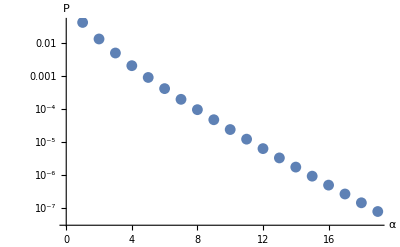

C:\Users\user\Dropbox\NYU\Grosberg\Code\Coloured_Noise\GO_PA_C.pdf

```mathematica
PPlot=ListLogPlot[
PList,
PlotRange->{All,Automatic},
AxesLabel->{Style["α",Bold,FontSize->16],Style["P",Bold,FontSize->16]},
TicksStyle->14,
GridLines->Automatic,
PlotLegends->Automatic]
Export[NotebookDirectory[]<>"GO_PA_C.pdf",%]
```

## Linear potential 2 shifting β

```mathematica
Δξ[θ_,θ0_,β_?NumericQ]:=β(Log[θ/θ0]-θ+θ0)
θ0[θ_,Δ_?NumericQ,β_?NumericQ]:=θ0/.FindRoot[Δξ[θ,θ0,β]==Δ,{θ0,1+θ}]//Re//Quiet
p0[θ0_,β_?NumericQ]:=√(β/(2π))Exp[-β/2 θ0^2]HeavisideTheta[θ0-1]
(* ρ is 2D PDF; pθ is marginalised over Δ *)
(*ρ[θ_,θ0_?NumericQ,β_?NumericQ]:=√((1-θ0)^2+θ0^2)θ0/(θ0-1)(θ-1)^2/(2 θ^2-2θ+1)*p0[θ0,β]//Re*)
ρ[θ_,θ0_?NumericQ,β_?NumericQ]:=θ0/(θ0+1)θ0/θ(1+1/θ)√(1+β^2(1-1/θ0)^2)*p0[θ0,β]//Re
pθ[θ_?NumericQ,β_?NumericQ]:=NIntegrate[ρ[θ,θ0[θ,δ,β],β],{δ,0,1}]
β=2;
ρPlot=ContourPlot[ρ[θ,θ0[θ,δ],β],
{δ,0,0.5},{θ,0,2},
PlotRange->All,
FrameLabel->{Style["x",Bold,FontSize->16],Style["η",Bold,FontSize->16]},
FrameTicksStyle->14,
PlotLegends->Automatic]
(*Export[NotebookDirectory[]<>"GO_PDF_C.pdf",%]*)
```

-Graphics-

```mathematica
PList=Table[NIntegrate[+1*ρ[θ,θ0[θ,δ,x],x],{δ,0,1.0},{θ,0,2}],{x,2,20,1}];
```

$Aborted

```mathematica
PPlot=ListLogPlot[
PList,
PlotRange->{All,Automatic},
AxesLabel->{Style["α",Bold,FontSize->16],Style["P",Bold,FontSize->16]},
TicksStyle->14,
GridLines->Automatic,
PlotLegends->Automatic]
Export[NotebookDirectory[]<>"GO_PA_C.pdf",%]
```

-Graphics-

C:\Users\user\Dropbox\NYU\Grosberg\Code\Coloured_Noise\GO_PA_C.pdf